### Лабораторная работа 6 Численное решение задачи Коши для ОДУ первого порядка и их систем Вариант 8

Задание 1. Решить задачу Коши для дифференциального уравнения первого порядка  
на отрезке [0, 1] :  
	а) методом Эйлера-Коши с шагом h_1= 0.1  и h_2= 0.05, построить графики 
полученных решений; 
	б) методом Рунге-Кутта 4-го порядка с шагом h_1= 0.1  и h_2= 0.05,
построить графики полученных решений; 
	в)  с помощью функций DSolve и NDSolve, построить графики. 
Сравнить все полученные решения. Cделать выводы о точности методов в 
зависимости от шага сетки. 

		1.8. y'-2x=y^2,  y(0) = 0.3.

```mathematica
Clear[x]; Clear[y];
f[x_,y_]=y^2+2x;
```

```mathematica
a=0; b=1; h1 = 0.1; h2=0.05; x0=0; y0=0.3;
```

а) Найдем число точек разбиения отрезка  n (не считая x_0):

```mathematica
n1 =Floor[(b-a)/h1]; n2 = Floor[(b-a)/h2]; x=x0; y=y0;
```

Составим таблицу приближенных значений функции y(x), вычисленных с помощью метода Эйлера-Коши:

Для h1:

```mathematica
eulk1=Table[{x,y}={x+h1, y+h1/2(f[x,y]+f[x+h1, y+h1*f[x,y]])},{i,n1}];
```

```mathematica
eulk1 =Prepend[eulk1,{x0,y0}]
```

{{0,0.3},{0.1,0.319274},{0.2,0.360477},{0.3,0.425522},{0.4,0.517258},{0.5,0.640105},{0.6,0.801096},{0.7,1.01172},{0.8,1.29154},{0.9,1.67589},{1.,2.23461}}

Изобразим полученное решение:

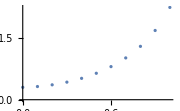

```mathematica
gr1=ListPlot[eulk1,ImageSize->Small]
```

Для h2:

```mathematica
x=x0; y=y0;
eulk2=Table[{x,y}={x+h2, y+h2/2(f[x,y]+f[x+h2, y+h2*f[x,y]])},{i,n2}];
```

```mathematica
eulk2 =Prepend[eulk2,{x0,y0}]
```

{{0,0.3},{0.05,0.307068},{0.1,0.319434},{0.15,0.337283},{0.2,0.36083},{0.25,0.390336},{0.3,0.426118},{0.35,0.468567},{0.4,0.518175},{0.45,0.575556},{0.5,0.641485},{0.55,0.716949},{0.6,0.803205},{0.65,0.90188},{0.7,1.01509},{0.75,1.14565},{0.8,1.29733},{0.85,1.4753},{0.9,1.68686},{0.95,1.94258},{1.,2.25833}}

Изобразим полученное решение:

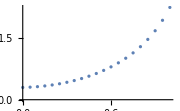

```mathematica
gr2=ListPlot[eulk2,ImageSize->Small]
```

б) Организуем цикл и создадим таблицу sol1 приближенных значений 
решения дифференциального уравнения, полученных с помощью метода Рунге-Кутта:

Для h1:

```mathematica
sol1=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n1+1,k++,
	k1[x_,y_]:=h1*f[x,y];
	k2[x_,y_]:=h1*f[x+h1/2,y+k1[x,y]/2];
	k3[x_,y_]:=h1*f[x+h1/2,y+k2[x,y]/2];
	k4[x_,y_]:=h1*f[x+h1,y+k3[x,y]];
	x=x+h1; y=y+ (k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
	sol1=Append[sol1,{x,y}]]
sol1
```

{{0,0.3},{0.1,0.340139},{0.2,0.403859},{0.3,0.493865},{0.4,0.614386},{0.5,0.772177},{0.6,0.978326},{0.7,1.25179},{0.8,1.62712},{0.9,2.17362},{1.,3.05225}}

Изобразим полученное решение:

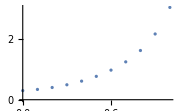

```mathematica
gr1=ListPlot[sol1,ImageSize->Small]
```

Для h2:

```mathematica
sol2=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n2+1,k++,
	k1[x_,y_]:=h2*f[x,y];
	k2[x_,y_]:=h2*f[x+h2/2,y+k1[x,y]/2];
	k3[x_,y_]:=h2*f[x+h2/2,y+k2[x,y]/2];
	k4[x_,y_]:=h2*f[x+h2,y+k3[x,y]];
	x=x+h2; y=y+ (k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
	sol2=Append[sol2,{x,y}]]
sol2
```

{{0,0.3},{0.05,0.312171},{0.1,0.32981},{0.15,0.353125},{0.2,0.382372},{0.25,0.417861},{0.3,0.459976},{0.35,0.509197},{0.4,0.566129},{0.45,0.631532},{0.5,0.706375},{0.55,0.791894},{0.6,0.889688},{0.65,1.00184},{0.7,1.13111},{0.75,1.28122},{0.8,1.45725},{0.85,1.66641},{0.9,1.91913},{0.95,2.23115},{1.,2.62732}}

Изобразим полученное решение:

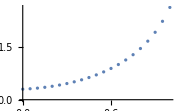

```mathematica
gr2=ListPlot[sol2,ImageSize->Small]
```

в) Решим данную задачу Коши с помощью функций DSolve и NDSolve.

```mathematica
Clear[x,y];
solD=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0}, y[x], x];
y1[x_]=y[x]/.Flatten[solD]
```

-((0.5 (1.41421 x^(3/2) BesselJ[-4/3,2/3 √2 x^(3/2)]-0.923823 x^(3/2) BesselJ[-2/3,2/3 √2 x^(3/2)]+1. BesselJ[-1/3,2/3 √2 x^(3/2)]-1.41421 x^(3/2) BesselJ[2/3,2/3 √2 x^(3/2)]))/(x (1. BesselJ[-1/3,2/3 √2 x^(3/2)]-0.326621 BesselJ[1/3,2/3 √2 x^(3/2)])))

```mathematica
solND=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0}, y[x], {x, 0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

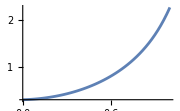

```mathematica
grD=Plot[y1[x], {x,0,1},ImageSize->Small]
```

```mathematica
grND = Plot[Evaluate[y[x]/.solND], {x,0,1}, ImageSize->Small]
```

-Graphics-

Метод Рунге-Кутта дает более точное приближенное решение, чем метод Эйлера-Коши. Чем меньше шаг, тем более точное решение получается.

Задание 2. Решить задачу Коши для дифференциального уравнения первого порядка  
на отрезке [0, 1] :  
	а) методом Эйлера с шагом h_1= 0.1  и h_2= 0.05, построить графики 
полученных решений; 
	б) методом Рунге-Кутта 4-го порядка с шагом h_1= 0.1  и h_2= 0.05,
построить графики полученных решений; 
	в)  с помощью функций DSolve и NDSolve, построить графики. 

		2.8. 		y’+5z-4y=0, y(0) =2.5,
				z’-3y+4z=0, z(0) =1.

```mathematica
Clear[y];
f[y_,z_]=4y-5z;
g[y_,z_,x_]=3y-4z;
y0=2.5; z0=1;
```

а) Метод Эйлера:

```mathematica
eulerMethod[{y0_,z0_},h_,n_]:= Module[{x=a,y=y0,z=z0,result={{x,y,z}}}, AppendTo[result,{x,y,z}]; For[i=1,i<=n,i++, y=y+h*f[y,z];
z=z+h*g[y,z,x];
x=x+h;
AppendTo[result,{x,y,z}];];
result];
```

Для h1:

```mathematica
eul1=eulerMethod[{y0,z0},h1,n1];
```

Изобразим полученное решение:

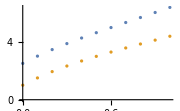

```mathematica
ListPlot[{eul1[[All,{1,2}]],eul1[[All,{1,3}]]},ImageSize->Small]
```

Для h2:

```mathematica
eul2=eulerMethod[{y0,z0},h2,n2];
```

Изобразим полученное решение:

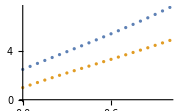

```mathematica
ListPlot[{eul2[[All,{1,2}]],eul2[[All,{1,3}]]},ImageSize->Small]
```

б) Метод Рунге-Кутта:

```mathematica
Clear[y,z];
rungeKuttaMethod[{y0_,z0_}, h_,n_]:=Module[{x=a,y=y0,z=z0,result={{x,y,z}}},AppendTo[result,{x,y,z}];
For[i=1,i<=n,i++,
{k1y,k1z}={h*f[y,z],h*g[y,z,x]};
{k2y,k2z}={h*f[y+k1y/2,z+k1z/2],h*g[y+k1y/2,z+k1z/2,x+h/2]};
{k3y,k3z}={h*f[y+k2y/2,z+k2z/2],h*g[y+k2y/2,z+k2z/2,x+h/2]};
{k4y,k4z}={h*f[y+k3y,z+k3z],h*g[y+k3y,z+k3z,x+h]};
y=y+(k1y+2*k2y+2*k3y+k4y)/6;
z=z+(k1z+2*k2z+2*k3z+k4z)/6;
x=x+h;
AppendTo[result,{x,y,z}];];
result];
```

Для h1:

```mathematica
rk1=rungeKuttaMethod[{y0,z0},h1,n1];
```

Изобразим полученное решение:

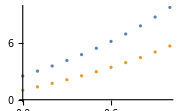

```mathematica
ListPlot[{rk1[[All,{1,2}]],rk1[[All,{1,3}]]},ImageSize->Small]
```

Для h2:

```mathematica
rk2=rungeKuttaMethod[{y0,z0},h2,n2];
```

Изобразим полученное решение:

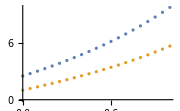

```mathematica
ListPlot[{rk2[[All,{1,2}]],rk2[[All,{1,3}]]},ImageSize->Small]
```

в) Решим данную задачу Коши с помощью функций DSolve и NDSolve.

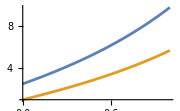

```mathematica
Clear[y,z];
eq1 =y'[x]+5z[x]-4y[x]==0;
eq2=z'[x]-3y[x]+4z[x]==0;
initialConditions={y[0]==2.5,z[0]==1};
solD=DSolve[{eq1,eq2,initialConditions}, {y,z}, x];
grD=Plot[{y[x]/.solD[[1]],z[x]/.solD[[1]]}, {x,0,1},ImageSize->Small]
```

```mathematica
solND=NDSolve[{eq1,eq2,initialConditions}, {y,z}, {x,0,1}];
```

```mathematica
grND=Plot[{y[x]/.solND,z[x]/.solND}, {x,0,1},ImageSize->Small]
```

-Graphics-